```mathematica
data = Import["/Users/gilbertodemelojr/Documents/UPM/2024-2/Estrutura de Dados II/apl2/APL-II---Estrutura-de-dados/resultados.csv", "CSV"];
```

```mathematica
Grid[data,Frame->All,Background->{{LightGray,White}},ItemStyle->Directive[Bold,FontSize->12]]
```

OPERACAO | TIPO_DE_ARVORE | ARVORE | TEMPO_NS | COMPARACOES
insercao | BST | BST #1 | 4572 | 8
insercao | AVL | AVL #1 | 11783 | 8
insercao | BST | BST #2 | 4947 | 6
insercao | AVL | AVL #2 | 7768 | 8
insercao | BST | BST #3 | 4786 | 9
insercao | AVL | AVL #3 | 8497 | 8
insercao | BST | BST #4 | 8781 | 6
insercao | AVL | AVL #4 | 8448 | 8
insercao | BST | BST #5 | 4968 | 8
insercao | AVL | AVL #5 | 7480 | 7
insercao | BST | BST #6 | 3601 | 6
insercao | AVL | AVL #6 | 5829 | 8
insercao | BST | BST #7 | 4242 | 12
insercao | AVL | AVL #7 | 4264 | 7
insercao | BST | BST #8 | 4821 | 8
insercao | AVL | AVL #8 | 11273 | 8
insercao | BST | BST #9 | 3881 | 6
insercao | AVL | AVL #9 | 6549 | 9
insercao | BST | BST #10 | 2947 | 6
insercao | AVL | AVL #10 | 6775 | 8
busca | BST | BST #1 | 5122 | 8
busca | AVL | AVL #1 | 1554 | 6
busca | BST | BST #2 | 2493 | 6
busca | AVL | AVL #2 | 1813 | 6
busca | BST | BST #3 | 2504 | 9
busca | AVL | AVL #3 | 12530 | 6
busca | BST | BST #4 | 1804 | 6
busca | AVL | AVL #4 | 1577 | 7
busca | BST | BST #5 | 8277 | 8
busca | AVL | AVL #5 | 1562 | 6
busca | BST | BST #6 | 3775 | 6
busca | AVL | AVL #6 | 1520 | 6
busca | BST | BST #7 | 4764 | 12
busca | AVL | AVL #7 | 1496 | 6
busca | BST | BST #8 | 2209 | 8
busca | AVL | AVL #8 | 1400 | 6
busca | BST | BST #9 | 1894 | 6
busca | AVL | AVL #9 | 1608 | 7
busca | BST | BST #10 | 1780 | 6
busca | AVL | AVL #10 | 447 | 7
remocao | BST | BST #1 | 3408 | 9
remocao | AVL | AVL #1 | 1490 | 7
remocao | BST | BST #2 | 2754 | 7
remocao | AVL | AVL #2 | 1333 | 7
remocao | BST | BST #3 | 2182 | 10
remocao | AVL | AVL #3 | 1699 | 7
remocao | BST | BST #4 | 1620 | 7
remocao | AVL | AVL #4 | 1474 | 8
remocao | BST | BST #5 | 1910 | 9
remocao | AVL | AVL #5 | 1288 | 7
remocao | BST | BST #6 | 1630 | 7
remocao | AVL | AVL #6 | 1289 | 7
remocao | BST | BST #7 | 6206 | 13
remocao | AVL | AVL #7 | 7262 | 7
remocao | BST | BST #8 | 1936 | 9
remocao | AVL | AVL #8 | 1277 | 7
remocao | BST | BST #9 | 1484 | 7
remocao | AVL | AVL #9 | 1364 | 8
remocao | BST | BST #10 | 1418 | 7
remocao | AVL | AVL #10 | 1429 | 8

```mathematica
headers = First[data];
```

```mathematica
dataRows = Rest[data];
```

## Operação de Inserção

```mathematica
opIndex = Position[headers, "OPERACAO"][[1, 1]];
```

```mathematica
insercao = Select[dataRows, #[[opIndex]] == "insercao" &];
```

```mathematica
Grid[Prepend[insercao,headers],Frame->All,Background->{{LightGray,White}},ItemStyle->Directive[FontSize->12]]
```

OPERACAO | TIPO_DE_ARVORE | ARVORE | TEMPO_NS | COMPARACOES
insercao | BST | BST #1 | 4572 | 8
insercao | AVL | AVL #1 | 11783 | 8
insercao | BST | BST #2 | 4947 | 6
insercao | AVL | AVL #2 | 7768 | 8
insercao | BST | BST #3 | 4786 | 9
insercao | AVL | AVL #3 | 8497 | 8
insercao | BST | BST #4 | 8781 | 6
insercao | AVL | AVL #4 | 8448 | 8
insercao | BST | BST #5 | 4968 | 8
insercao | AVL | AVL #5 | 7480 | 7
insercao | BST | BST #6 | 3601 | 6
insercao | AVL | AVL #6 | 5829 | 8
insercao | BST | BST #7 | 4242 | 12
insercao | AVL | AVL #7 | 4264 | 7
insercao | BST | BST #8 | 4821 | 8
insercao | AVL | AVL #8 | 11273 | 8
insercao | BST | BST #9 | 3881 | 6
insercao | AVL | AVL #9 | 6549 | 9
insercao | BST | BST #10 | 2947 | 6
insercao | AVL | AVL #10 | 6775 | 8

```mathematica
insercao = Prepend[insercao, headers];
```

### BST

```mathematica
opIndex = Position[headers, "TIPO_DE_ARVORE"][[1, 1]];
```

```mathematica
BSTprev= Select[Rest[insercao], #[[opIndex]] == "BST" &];
```

```mathematica
BST = Prepend[BSTprev, headers];
```

```mathematica
Grid[BST,Frame->All,Background->{{LightGray,White}},ItemStyle->Directive[FontSize->12]]
```

OPERACAO | TIPO_DE_ARVORE | ARVORE | TEMPO_NS | COMPARACOES
insercao | BST | BST #1 | 4572 | 8
insercao | BST | BST #2 | 4947 | 6
insercao | BST | BST #3 | 4786 | 9
insercao | BST | BST #4 | 8781 | 6
insercao | BST | BST #5 | 4968 | 8
insercao | BST | BST #6 | 3601 | 6
insercao | BST | BST #7 | 4242 | 12
insercao | BST | BST #8 | 4821 | 8
insercao | BST | BST #9 | 3881 | 6
insercao | BST | BST #10 | 2947 | 6

```mathematica
indiceColuna = Position[First[BST], "TEMPO_NS"][[1, 1]];
```

```mathematica
somaTempo = Total[Rest[BST][[All, indiceColuna]]];
```

```mathematica
media = somaTempo / Length[Rest[BST]];
```

```mathematica
Print[Style["A média em de inserção de um nó na BST é: "<>ToString[N[media]] <> " ns.",Background->LightYellow,FontColor->Black,FontSize->14,Bold ]]
```

A média em de inserção de um nó na BST é: 4754.6 ns.

```mathematica
(* Gráfico de barras do tempo de inserção *)
```

```mathematica
indiceArvore = Position[First[BST], "ARVORE"][[1, 1]];
```

```mathematica
indiceTempo = Position[First[BST], "TEMPO_NS"][[1, 1]];
```

```mathematica
rotulosArvore = Rest[BST][[All, indiceArvore]];
```

```mathematica
valoresTempo = Rest[BST][[All, indiceTempo]];
```

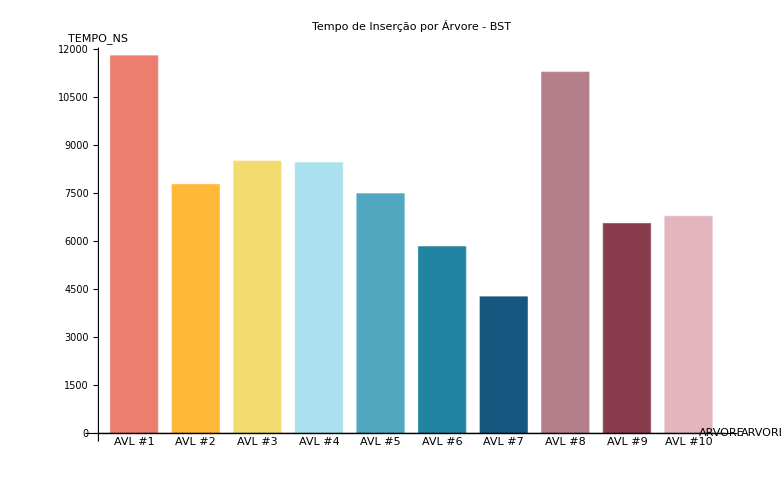

```mathematica
BarChart[valoresTempo, ChartLabels->Placed[rotulosArvore,Below], AxesLabel-> {"ARVORE", "TEMPO_NS"}, ChartStyle-> 24, BarSpacing->0.3, PlotLabel->Style["Tempo de Inserção por Árvore - BST", Bold]]
```

### AVL

```mathematica
opIndex = Position[headers, "TIPO_DE_ARVORE"][[1, 1]];
```

```mathematica
AVLprev= Select[Rest[insercao], #[[opIndex]] == "AVL" &];
```

```mathematica
AVL= Prepend[AVLprev, headers];
```

```mathematica
Grid[AVL,Frame->All,Background->{{LightGray,White}},ItemStyle->Directive[FontSize->12]]
```

OPERACAO | TIPO_DE_ARVORE | ARVORE | TEMPO_NS | COMPARACOES
insercao | AVL | AVL #1 | 11783 | 8
insercao | AVL | AVL #2 | 7768 | 8
insercao | AVL | AVL #3 | 8497 | 8
insercao | AVL | AVL #4 | 8448 | 8
insercao | AVL | AVL #5 | 7480 | 7
insercao | AVL | AVL #6 | 5829 | 8
insercao | AVL | AVL #7 | 4264 | 7
insercao | AVL | AVL #8 | 11273 | 8
insercao | AVL | AVL #9 | 6549 | 9
insercao | AVL | AVL #10 | 6775 | 8

```mathematica
indiceColuna = Position[First[AVL], "TEMPO_NS"][[1, 1]];
```

```mathematica
somaTempo = Total[Rest[AVL][[All, indiceColuna]]];
```

```mathematica
media = somaTempo / Length[Rest[AVL]];
```

```mathematica
Print[Style["A média em de inserção de um nó na AVL é: "<>ToString[N[media]] <> " ns.",Background->LightYellow,FontColor->Black,FontSize->14,Bold ]]
```

A média em de inserção de um nó na AVL é: 7866.6 ns.

```mathematica
indiceArvore = Position[First[AVL], "ARVORE"][[1, 1]];
```

```mathematica
indiceTempo = Position[First[AVL], "TEMPO_NS"][[1, 1]];
```

```mathematica
rotulosArvore = Rest[AVL][[All, indiceArvore]];
```

```mathematica
valoresTempo = Rest[AVL][[All, indiceTempo]];
```

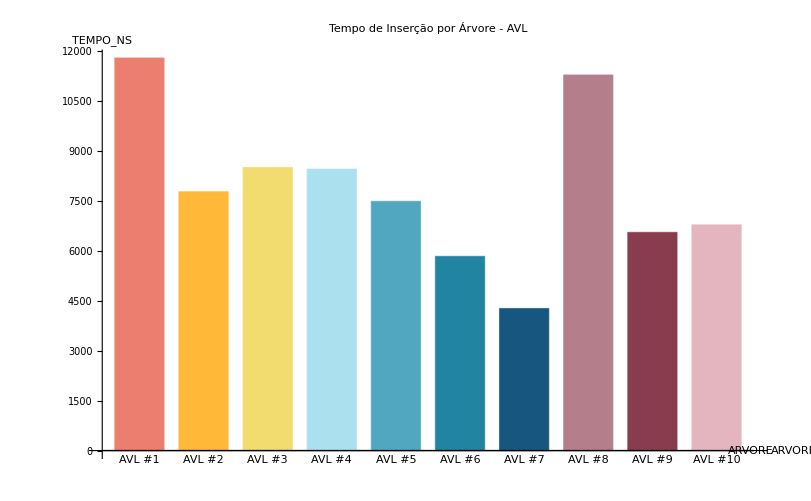

```mathematica
BarChart[valoresTempo, ChartLabels-> Placed[rotulosArvore,Below], AxesLabel-> {"ARVORE", "TEMPO_NS"}, ChartStyle-> 24, BarSpacing->0.3, PlotLabel->Style["Tempo de Inserção por Árvore - AVL", Bold]]
```